```mathematica
Gds={{-2/r^4-λ-(2 Csc[θ]^2)/r^4+1/2 (-2-3/r^4-4/r^2-Cot[θ]^2-Csc[θ]^2-(2 Csc[θ]^2)/r^4-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4),0,0,0,0},{0,-2/r^2-λ/r^2-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4+(-2-3/r^4-4/r^2-Cot[θ]^2-Csc[θ]^2-(2 Csc[θ]^2)/r^4-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4)/(2 r^2),0,0,0},{0,0,-1/r^4-2/r^2-Cot[θ]^2-Csc[θ]^2-(λ Csc[θ]^2)/r^2+(Csc[θ]^2 (-2-3/r^4-4/r^2-Cot[θ]^2-Csc[θ]^2-(2 Csc[θ]^2)/r^4-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4))/(2 r^2),0,0},{0,0,0,-1+λ/c^2-(-2-3/r^4-4/r^2-Cot[θ]^2-Csc[θ]^2-(2 Csc[θ]^2)/r^4-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4)/(2 c^2),0},{0,0,0,0,-1-λ/c^2+(-2-3/r^4-4/r^2-Cot[θ]^2-Csc[θ]^2-(2 Csc[θ]^2)/r^4-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4)/(2 c^2)}}
```

{{-2/r^4-λ-(2 Csc[θ]^2)/r^4+1/2 (-2-3/r^4-4/r^2-Cot[θ]^2-Csc[θ]^2-(2 Csc[θ]^2)/r^4-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4),0,0,0,0},{0,-2/r^2-λ/r^2-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4+(-2-3/r^4-4/r^2-Cot[θ]^2-Csc[θ]^2-(2 Csc[θ]^2)/r^4-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4)/(2 r^2),0,0,0},{0,0,-1/r^4-2/r^2-Cot[θ]^2-Csc[θ]^2-(λ Csc[θ]^2)/r^2+(Csc[θ]^2 (-2-3/r^4-4/r^2-Cot[θ]^2-Csc[θ]^2-(2 Csc[θ]^2)/r^4-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4))/(2 r^2),0,0},{0,0,0,-1+1.11265×10^-21 λ-5.56325×10^-22 (-2-3/r^4-4/r^2-Cot[θ]^2-Csc[θ]^2-(2 Csc[θ]^2)/r^4-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4),0},{0,0,0,0,-1-1.11265×10^-21 λ+5.56325×10^-22 (-2-3/r^4-4/r^2-Cot[θ]^2-Csc[θ]^2-(2 Csc[θ]^2)/r^4-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4)}}

```mathematica
Gads={{-2/r^4-λ-(2 Csc[θ]^2)/r^4,0,0,0,0},{0,-2/r^2-λ/r^2-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4,0,0,0},{0,0,-1/r^4-2/r^2-Cot[θ]^2-Csc[θ]^2-(λ Csc[θ]^2)/r^2,0,0},{0,0,0,-1+λ/c^2,0},{0,0,0,0,-1+λ/c^2}}
```

{{-2/r^4-λ-(2 Csc[θ]^2)/r^4,0,0,0,0},{0,-2/r^2-λ/r^2-(Csc[θ]^2 (1+r^4 Cot[θ]^2+r^4 Csc[θ]^2))/r^4,0,0,0},{0,0,-1/r^4-2/r^2-Cot[θ]^2-Csc[θ]^2-(λ Csc[θ]^2)/r^2,0,0},{0,0,0,-1+1.11265×10^-21 λ,0},{0,0,0,0,-1+1.11265×10^-21 λ}}

```mathematica
Gdu=FullSimplify[ExpandAll[Gds.Gads]]
```

{{((2+r^4 λ+2 Csc[θ]^2) (7+4 r^2+r^4 (1+2 λ)+(7+r^4) Csc[θ]^2+2 r^4 Csc[θ]^4))/(2 r^8),0,0,0,0},{0,1/(2 r^10)(r^2 (2+λ)-(-1+r^4) Csc[θ]^2+2 r^4 Csc[θ]^4) (3+4 r^2+r^4 (5+2 λ)+(3+2 r^2+r^4-2 r^6) Csc[θ]^2+2 (r^4+2 r^6) Csc[θ]^4),0,0,0},{0,0,1/(2 r^10)(1+2 r^2+r^4 Cot[θ]^2+r^2 (r^2+λ) Csc[θ]^2) (2 r^2+4 r^4-2 r^6+(3+4 r^2+4 r^6+r^4 (1+2 λ)) Csc[θ]^2+(3+r^4) Csc[θ]^4+2 r^4 Csc[θ]^6),0,0},{0,0,0,1/r^4(-1.66898×10^-21+r^2 (-2.2253×10^-21+2.47598×10^-42 λ)+1.85699×10^-42 λ+r^4 (1.+(-2.2253×10^-21+1.23799×10^-42 λ) λ)-1.66898×10^-21 Csc[θ]^2+(r^4 (-1.18219×10^-21+1.31536×10^-42 λ)+9.28493×10^-43 λ-9.28493×10^-43 λ Cos[2 θ]+r^4 (6.95406×10^-23-7.73744×10^-44 λ) Cos[4 θ]) Csc[θ]^4),0},{0,0,0,0,1/r^4(1.66898×10^-21+r^2 (2.2253×10^-21-2.47598×10^-42 λ)-1.85699×10^-42 λ+r^4 (1.-1.23799×10^-42 λ^2)+1.66898×10^-21 Csc[θ]^2+(r^4 (1.18219×10^-21-1.31536×10^-42 λ)-9.28493×10^-43 λ+9.28493×10^-43 λ Cos[2 θ]+r^4 (-6.95406×10^-23+7.73744×10^-44 λ) Cos[4 θ]) Csc[θ]^4)}}

```mathematica
TensorContract[Gdu,{{1,2}}]
```

((2+r^4 λ+2 Csc[θ]^2) (7+4 r^2+r^4 (1+2 λ)+(7+r^4) Csc[θ]^2+2 r^4 Csc[θ]^4))/(2 r^8)+1/(2 r^10)(r^2 (2+λ)-(-1+r^4) Csc[θ]^2+2 r^4 Csc[θ]^4) (3+4 r^2+r^4 (5+2 λ)+(3+2 r^2+r^4-2 r^6) Csc[θ]^2+2 (r^4+2 r^6) Csc[θ]^4)+1/r^4(-1.66898×10^-21+r^2 (-2.2253×10^-21+2.47598×10^-42 λ)+1.85699×10^-42 λ+r^4 (1.+(-2.2253×10^-21+1.23799×10^-42 λ) λ)-1.66898×10^-21 Csc[θ]^2+(r^4 (-1.18219×10^-21+1.31536×10^-42 λ)+9.28493×10^-43 λ-9.28493×10^-43 λ Cos[2 θ]+r^4 (6.95406×10^-23-7.73744×10^-44 λ) Cos[4 θ]) Csc[θ]^4)+1/r^4(1.66898×10^-21+r^2 (2.2253×10^-21-2.47598×10^-42 λ)-1.85699×10^-42 λ+r^4 (1.-1.23799×10^-42 λ^2)+1.66898×10^-21 Csc[θ]^2+(r^4 (1.18219×10^-21-1.31536×10^-42 λ)-9.28493×10^-43 λ+9.28493×10^-43 λ Cos[2 θ]+r^4 (-6.95406×10^-23+7.73744×10^-44 λ) Cos[4 θ]) Csc[θ]^4)+1/(2 r^10)(1+2 r^2+r^4 Cot[θ]^2+r^2 (r^2+λ) Csc[θ]^2) (2 r^2+4 r^4-2 r^6+(3+4 r^2+4 r^6+r^4 (1+2 λ)) Csc[θ]^2+(3+r^4) Csc[θ]^4+2 r^4 Csc[θ]^6)

```mathematica
c=2.99792458*10^(10)
```

2.99792×10^10

```mathematica
wr=Table[r/.Solve[((c^2-λ) (3+4 r^2+r^4 (1+2 c^2+2 λ)+(3+r^4) Csc[θ]^2+2 r^4 Csc[θ]^4))/(2 c^4 r^4)+((2+r^4 λ+2 Csc[θ]^2) (7+4 r^2+r^4 (1+2 λ)+(7+r^4) Csc[θ]^2+2 r^4 Csc[θ]^4))/(2 r^8)+1/(2 r^10)(r^2 (2+λ)-(-1+r^4) Csc[θ]^2+2 r^4 Csc[θ]^4) (3+4 r^2+r^4 (5+2 λ)+(3+2 r^2+r^4-2 r^6) Csc[θ]^2+2 (r^4+2 r^6) Csc[θ]^4)+1/(2 r^10)(1+2 r^2+r^4 Cot[θ]^2+r^2 (r^2+λ) Csc[θ]^2) (2 r^2+4 r^4-2 r^6+(3+4 r^2+4 r^6+r^4 (1+2 λ)) Csc[θ]^2+(3+r^4) Csc[θ]^4+2 r^4 Csc[θ]^6)+((c^2-λ) (-3-4 r^2+r^4 (-1+2 c^2-2 λ)-Csc[θ]^2 (3+r^4+2 r^4 Csc[θ]^2)))/(2 c^4 r^4)==0,r],{θ,-N[Pi]-0.01,N[Pi],Pi/128}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
Dimensions[wr]
```

{257,10}

```mathematica
Length[wr]
```

257

```mathematica
wrr=Flatten[wr/.λ->0];
```

```mathematica
Length[wrr]
```

2570

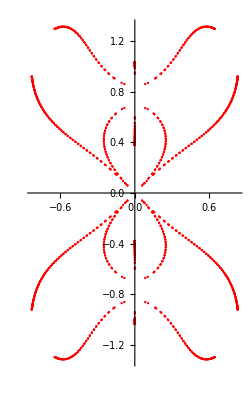

```mathematica
ComplexListPlot[wrr,PlotStyle->Red,ImageSize->Full]
```